```mathematica
SetDirectory["/Users/Mukesh/Documents/Research/RSD"]
```

/Users/Mukesh/Documents/Research/RSD

```mathematica
da=ReadList["hydra_matterpower_z0.dat",{Number,Number}];
kCAMB=Flatten[Drop[da,{},{2,2}]];
PkCAMB=Flatten[Drop[da,{},{1,1}]];
PlinHydra=Interpolation[da];
```

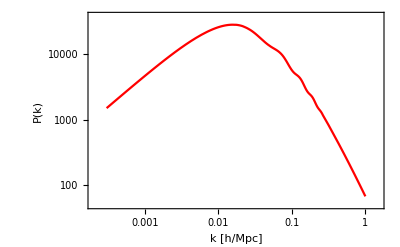

```mathematica
LogLogPlot[PlinHydra[k],{k,0.0003,1},Frame->True,PlotStyle->Red,LabelStyle->{Italic,FontFamily->"Helvetica"},FrameLabel->{"k [h/Mpc]","P(k)"},ColorFunctionScaling->False,ImageSize->400,FrameTicksStyle->20,FrameStyle->21]
```

```mathematica
xs = ReadList["xs.dat", {Number,Number,Number}]
```

{{1,63,73},{1,63,74},{1,63,75},{1,63,76},{1,63,77},{1,64,70},{1,64,71},{1,64,72},{1,64,73},{1,64,74},{1,64,75},{1,64,76},{1,64,77},{1,64,78},{1,64,79},{1,64,80},{1,65,69},{1,65,70},{1,65,71},{1,65,72},{1,65,73},1766272,{149,85,78},{149,85,79},{149,85,80},{149,85,81},{149,86,70},{149,86,71},{149,86,72},{149,86,73},{149,86,74},{149,86,75},{149,86,76},{149,86,77},{149,86,78},{149,86,79},{149,86,80},{149,87,73},{149,87,74},{149,87,75},{149,87,76},{149,87,77}}
 |  |  |  |

```mathematica
L=150;
Ng = Length[xs];Ng
d = {0,0,L}
```

1766313

{0,0,150}

```mathematica
rs = Table[Normalize[xs[[i]]+d],{i,Ng}]
```

{{1/(√53699),63/(√53699),223/(√53699)},{1/(√54146),63/(√54146),112 √(2/27073)},{1/(√54595),63/(√54595),45 √(5/10919)},{1/(√55046),63/(√55046),113 √(2/27523)},{1/(√55499),63/(√55499),227/(√55499)},{1/(3 √5833),64/(3 √5833),220/(3 √5833)},{1/(3 √5882),(32 √(2/2941))/3,(13 √(17/346))/3},{1/(√53381),64/(√53381),222/(√53381)},1766297,{149/(√81581),86/(√81581),228/(√81581)},{149/(11 √678),(43 √(2/339))/11,229/(11 √678)},{149/(√82497),86/(√82497),230/(√82497)},{149/(√79499),87/(√79499),223/(√79499)},{149/(√79946),87/(√79946),112 √(2/39973)},{149/(√80395),87/(√80395),45 √(5/16079)},{149/(√80846),87/(√80846),113 √(2/40423)},{149/(√81299),87/(√81299),227/(√81299)}}
 |  |  |  |

```mathematica
a=0;JS[k1_,k2_] := Do[a=a+N[(1/Ng)(k1.rs[[j]])^2];,{j,1,Ng}]
```

```mathematica
J[{0,1,0},{0,-1,0}]
```

```mathematica
a
```

0.103955

```mathematica
a
```

0.792091

```mathematica
a
```

0.792098

```mathematica
a=0;J[k1_,k2_] := Do[a=a-N[(1/Ng)(k1.rs[[j]])*(k2.rs[[j]])*Exp[-ⅈ*((k1+k2).xs[[j]])]];,{j,1,Ng}]
```